```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
changeNK[2, 2]
```

```mathematica
H = Sum[p[i, a]p[i, a], {a, 1, ($N)^2-1}, {i, 1, $K}] + 1/8 Sum[With[{xi = Array[x[i, #]&, ($N)^2-1], xj = Array[x[j, #]&, ($N)^2-1]},#.#&@comm[xi, xj, $fSU]], {i, 1, $K}, {j, 1, $K}]
```

p[1,1]^2+p[1,2]^2+p[1,3]^2+p[2,1]^2+p[2,2]^2+p[2,3]^2+1/8 ((x[1,2] x[2,1]-x[1,1] x[2,2])^2+(-x[1,2] x[2,1]+x[1,1] x[2,2])^2+(x[1,3] x[2,1]-x[1,1] x[2,3])^2+(-x[1,3] x[2,1]+x[1,1] x[2,3])^2+(x[1,3] x[2,2]-x[1,2] x[2,3])^2+(-x[1,3] x[2,2]+x[1,2] x[2,3])^2)

```mathematica
H = H//FullSimplify
```

p[1,1]^2+p[1,2]^2+p[1,3]^2+p[2,1]^2+p[2,2]^2+p[2,3]^2+1/4 (x[1,3]^2 (x[2,1]^2+x[2,2]^2)-2 x[1,1] x[1,3] x[2,1] x[2,3]-2 x[1,2] x[2,2] (x[1,1] x[2,1]+x[1,3] x[2,3])+x[1,2]^2 (x[2,1]^2+x[2,3]^2)+x[1,1]^2 (x[2,2]^2+x[2,3]^2))

```mathematica
intparams = Flatten[Join[Array[{x[#1, #2], -Λ, ∞}&, {$K, ($N)^2-1}], Array[{p[#1, #2], -∞, ∞}&, {$K, ($N)^2-1}]], 1]
```

{{x[1,1],-∞,∞},{x[1,2],-∞,∞},{x[1,3],-∞,∞},{x[2,1],-∞,∞},{x[2,2],-∞,∞},{x[2,3],-∞,∞},{p[1,1],-∞,∞},{p[1,2],-∞,∞},{p[1,3],-∞,∞},{p[2,1],-∞,∞},{p[2,2],-∞,∞},{p[2,3],-∞,∞}}

```mathematica
Integrate[Exp[-H] x[1, 1]^2, Sequence@@intparams]
```

Integrate::idiv: Integral of (4 π^4 Abs[x[1,1]])/(√(x[1,1]^2+x[1,2]^2+x[1,3]^2)) does not converge on {-∞,∞}.

Integrate::idiv: Integral of Abs[x[1,1]]/(√(x[1,1]^2+x[1,2]^2+x[1,3]^2)) does not converge on {-∞,∞}.

4 π^4 ∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ Abs[x[1,1]]/(√(x[1,1]^2+x[1,2]^2+x[1,3]^2))ⅆx[2,1]ⅆx[1,3]ⅆx[1,2]ⅆx[1,1]

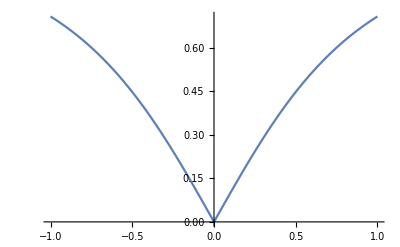

```mathematica
Plot[Abs[x]/(√(x^2+1)), {x, -1, 1}]
```

```mathematica
Integrate[Abs[x]/(√(x^2+1)), {x, -∞, ∞}, PrincipalValue->True]
```

Integrate::idiv: Integral of Abs[x]/(√(1+x^2)) does not converge on {-∞,∞}.

Integrate[Abs[x]/(√(1+x^2)),{x,-∞,∞},PrincipalValue→True]